```mathematica
Wout[0,m_]:={1}
```

```mathematica
Wout[0,10]
```

1

```mathematica
LastVar=1
```

1

```mathematica
NewVar[]:=Indexed[x,LastVar++]
```

```mathematica
Wout[n_,m_]:=Union[
Flatten[
Table[
Union[
Map[#+(Mod[-m,6])+6b+2*3^(n-1)NewVar[]&,Wout[n-1,Mod[m+1+2b,2*3^(n-1)]]],
Map[#+(Mod[2-m,6])+6b+2*3^(n-1)NewVar[]&,Wout[n-1,Mod[m+2+2b,2*3^(n-1)]]]
],
{b,0,3^(n-2)-1}
]
],
{1},
{(Mod[(4-m),6]+6NewVar[])}
]
```

```mathematica
LastVar=1;Wout[3,1]//TableForm
```

1
6+18 x8
10+6 x2+18 x9
10+6 x1+6 x3+18 x10
6+6 x5+18 x11
5+6 x4+6 x6+18 x12
7+6 x7+18 x13
2+18 x21
5+6 x15+18 x22
4+6 x14+6 x16+18 x23
7+6 x18+18 x24
11+6 x17+6 x19+18 x25
2+6 x20+18 x26
12+18 x34
14+6 x28+18 x35
18+6 x27+6 x29+18 x36
16+6 x31+18 x37
19+6 x30+6 x32+18 x38
11+6 x33+18 x39
8+18 x47
9+6 x41+18 x48
12+6 x40+6 x42+18 x49
11+6 x44+18 x50
13+6 x43+6 x45+18 x51
12+6 x46+18 x52
18+18 x60
18+6 x54+18 x61
20+6 x53+6 x55+18 x62
20+6 x57+18 x63
21+6 x56+6 x58+18 x64
21+6 x59+18 x65
14+18 x73
19+6 x67+18 x74
20+6 x66+6 x68+18 x75
15+6 x70+18 x76
15+6 x69+6 x71+18 x77
16+6 x72+18 x78
3+6 x79

```mathematica
Sin +1
```

1+Sin

```mathematica
Table[LastVar=1;Wout[max,1]//Length,{max,2,5}]
```

{6,38,686,37046}

```mathematica
LastVar=1;Wout[2,1]//TableForm
```

1
6+6 x2
7+6 x1+6 x3
2+6 x5
2+6 x4+6 x6
3+6 x7

```mathematica
LastVar=1;Map[Framed,Wout[2,1]]//Multicolumn
```

1 | 7+6 x1+6 x3 | 2+6 x4+6 x6
6+6 x2 | 2+6 x5 | 3+6 x7

```mathematica
LastVar=1;Map[ListofVars,Wout[2,1]]//TableForm
```

| 
x2 | 
x1 | x3
x5 | 
x4 | x6
x7 |

```mathematica
IterateSome[form_]:=Block[{vars=ListofVars[form],res},
If[vars=={},
{form},
Map[IterateSome,Table[(form/.vars[[1]]->k),{k,1,30}]]
]
]
```

```mathematica
IterateSome2[form_, count_]:=Block[{vars=ListofVars[form],res},
If[vars=={},
{form},
Map[IterateSome2[#,count]&,Table[(form/.vars[[1]]->k),{k,1,count}]]
]
]
```

```mathematica
Plot3D[{7+6 x+6 y,2+6 x+6 y},{x,1,10},{y,1,10}]
```

-Graphics3D-

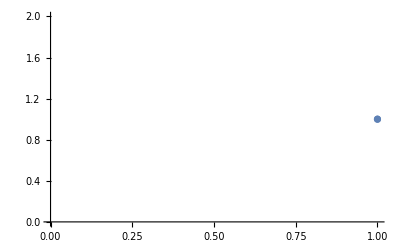
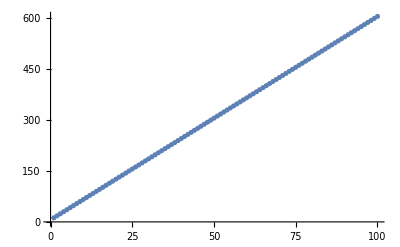
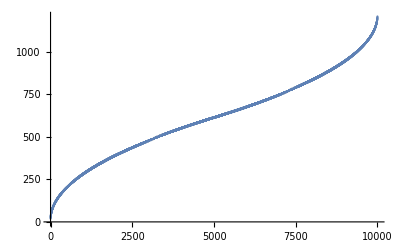
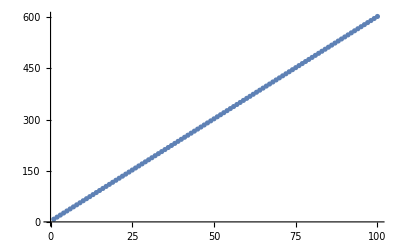
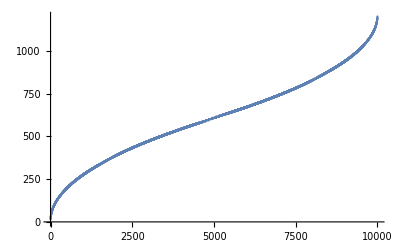
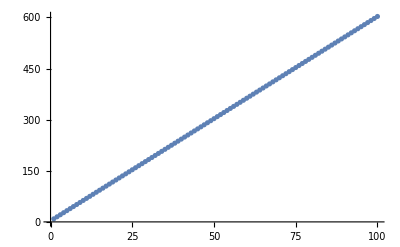
{-Graphics-1,-Graphics-6+6 x2,-Graphics-7+6 x1+6 x3,-Graphics-2+6 x5,-Graphics-2+6 x4+6 x6,-Graphics-3+6 x7}

```mathematica
LastVar=1;Map[With[{form=IterateSome2[#,100]},Labeled[ListPlot[Sort[Flatten[form]]],#]]&,Wout[2,1]]
```

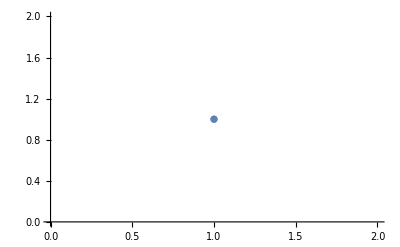
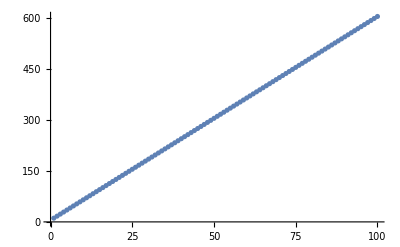
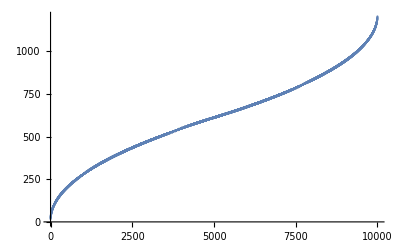
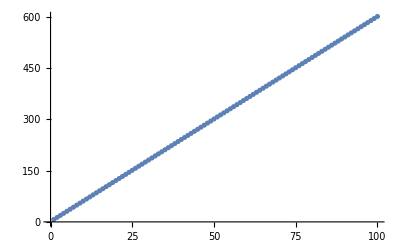
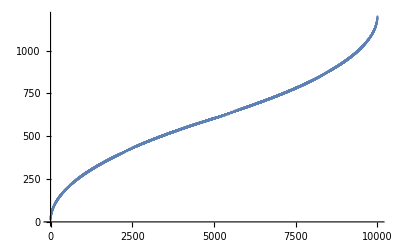
{-Graphics-1,-Graphics-5+6 x2,-Graphics-5+6 x1+6 x3,-Graphics-1+6 x5,-Graphics-6 x4+6 x6,-Graphics-2+6 x7}

```mathematica
LastVar=1;Map[With[{form=IterateSome2[#,100]},Labeled[ListPlot[Sort[Flatten[form]],PlotRange->All],#]]&,Wout[2,8]]
```

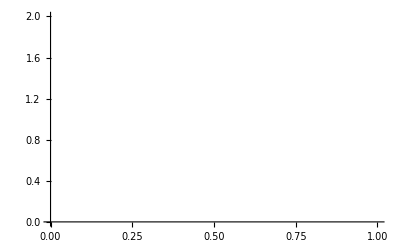
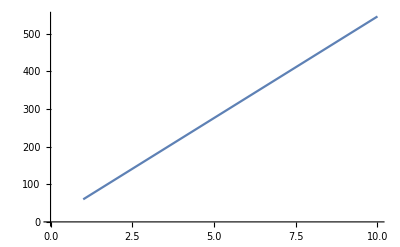
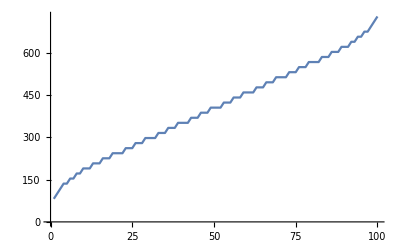
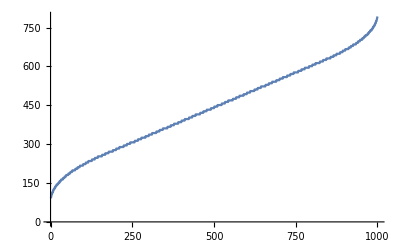
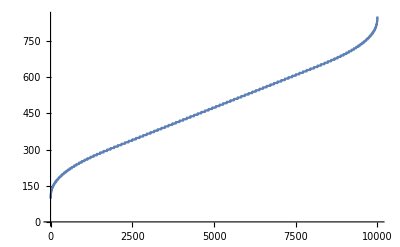
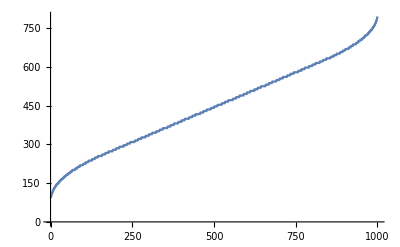
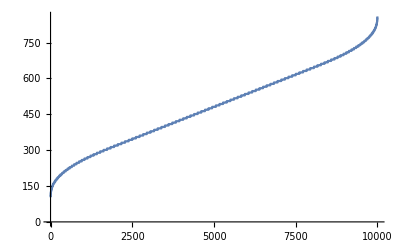
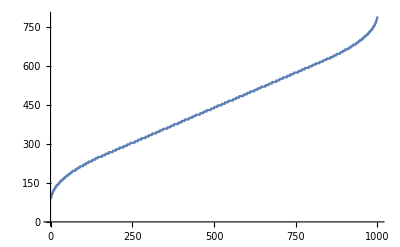
{-Graphics-1,-Graphics-6+54 x80,-Graphics-10+18 x8+54 x81,-Graphics-13+6 x2+18 x9+54 x82,-Graphics-12+6 x1+6 x3+18 x10+54 x83,-Graphics-15+6 x5+18 x11+54 x84,-Graphics-19+6 x4+6 x6+18 x12+54 x85,-Graphics-10+6 x7+18 x13+54 x86,-Graphics-6+18 x21+54 x87,-Graphics-8+6 x15+18 x22+54 x88}

```mathematica
LastVar=1;Map[With[{form=IterateSome2[#,10]},Labeled[ListLinePlot[Sort[Flatten[form]]],#]]&,Take[Wout[4,1],10]]
```

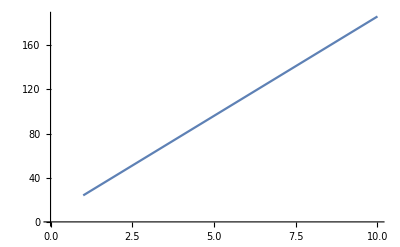
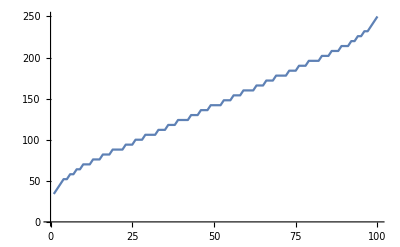
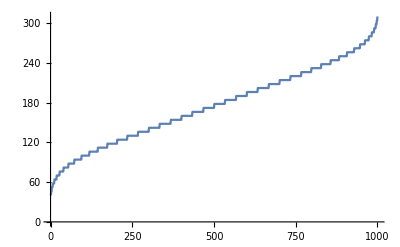
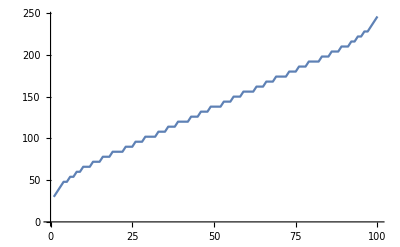
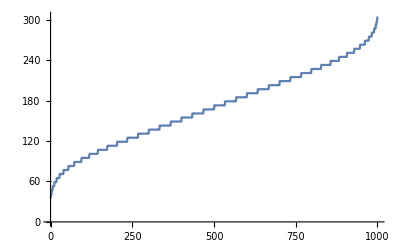
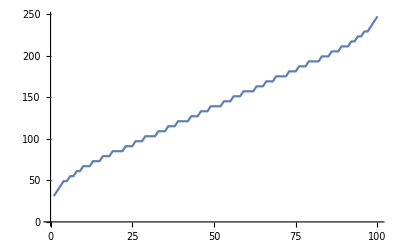
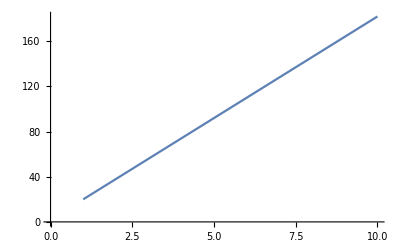
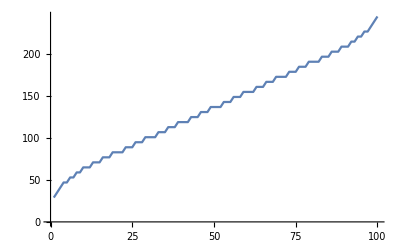
{-Graphics-1,-Graphics-6+18 x8,-Graphics-10+6 x2+18 x9,-Graphics-10+6 x1+6 x3+18 x10,-Graphics-6+6 x5+18 x11,-Graphics-5+6 x4+6 x6+18 x12,-Graphics-7+6 x7+18 x13,-Graphics-2+18 x21,-Graphics-5+6 x15+18 x22,-Graphics-4+6 x14+6 x16+18 x23,-Graphics-7+6 x18+18 x24,-Graphics-11+6 x17+6 x19+18 x25,-Graphics-2+6 x20+18 x26,-Graphics-12+18 x34,-Graphics-14+6 x28+18 x35,-Graphics-18+6 x27+6 x29+18 x36,-Graphics-16+6 x31+18 x37,-Graphics-19+6 x30+6 x32+18 x38,-Graphics-11+6 x33+18 x39,-Graphics-8+18 x47,-Graphics-9+6 x41+18 x48,-Graphics-12+6 x40+6 x42+18 x49,-Graphics-11+6 x44+18 x50,-Graphics-13+6 x43+6 x45+18 x51,-Graphics-12+6 x46+18 x52,-Graphics-18+18 x60,-Graphics-18+6 x54+18 x61,-Graphics-20+6 x53+6 x55+18 x62,-Graphics-20+6 x57+18 x63,-Graphics-21+6 x56+6 x58+18 x64,-Graphics-21+6 x59+18 x65,-Graphics-14+18 x73,-Graphics-19+6 x67+18 x74,-Graphics-20+6 x66+6 x68+18 x75,-Graphics-15+6 x70+18 x76,-Graphics-15+6 x69+6 x71+18 x77,-Graphics-16+6 x72+18 x78,-Graphics-3+6 x79}

```mathematica
LastVar=1;Map[With[{form=IterateSome[#]},Labeled[ListLinePlot[Sort[Flatten[form]]],#]]&,Wout[3,1]]
```

```mathematica
LastVar=1;Map[Framed,Wout[4,1]]//Multicolumn
```

1 | 22+18 x60+54 x105 | 11+18 x151+54 x210 | 14+18 x242+54 x315 | 28+6 x287+6 x289+18 x296+54 x341 | 19+6 x378+6 x380+18 x387+54 x446 | 24+6 x469+6 x471+18 x478+54 x551 | 35+6 x524+6 x526+18 x532+54 x577 | 32+6 x615+6 x617+18 x623+54 x682 | 37+6 x706+6 x708+18 x714+54 x787 | 36+18 x775+54 x813 | 31+18 x866+54 x918 | 34+18 x957+54 x1023 | 52+6 x1002+6 x1004+18 x1011+54 x1049 | 37+6 x1093+6 x1095+18 x1102+54 x1154 | 42+6 x1184+6 x1186+18 x1193+54 x1259 | 53+6 x1239+6 x1241+18 x1247+54 x1285 | 44+6 x1330+6 x1332+18 x1338+54 x1390 | 49+6 x1421+6 x1423+18 x1429+54 x1495 | 43+6 x1483+54 x1521 | 53+18 x1581+54 x1626 | 56+18 x1672+54 x1731 | 45+18 x1763+54 x1836 | 63+6 x1808+6 x1810+18 x1817+54 x1862 | 62+6 x1899+6 x1901+18 x1908+54 x1967 | 59+6 x1990+6 x1992+18 x1999+54 x2072 | 70+6 x2045+6 x2047+18 x2053+54 x2098
6+54 x80 | 27+6 x54+18 x61+54 x106 | 11+6 x145+18 x152+54 x211 | 15+6 x236+18 x243+54 x316 | 31+6 x291+18 x297+54 x342 | 15+6 x382+18 x388+54 x447 | 19+6 x473+18 x479+54 x552 | 34+6 x527+18 x533+54 x578 | 24+6 x618+18 x624+54 x683 | 28+6 x709+18 x715+54 x788 | 40+6 x769+18 x776+54 x814 | 36+6 x860+18 x867+54 x919 | 34+6 x951+18 x958+54 x1024 | 50+6 x1006+18 x1012+54 x1050 | 40+6 x1097+18 x1103+54 x1155 | 38+6 x1188+18 x1194+54 x1260 | 53+6 x1242+18 x1248+54 x1286 | 43+6 x1333+18 x1339+54 x1391 | 41+6 x1424+18 x1430+54 x1496 | 38+54 x1601 | 57+6 x1575+18 x1582+54 x1627 | 61+6 x1666+18 x1673+54 x1732 | 45+6 x1757+18 x1764+54 x1837 | 61+6 x1812+18 x1818+54 x1863 | 65+6 x1903+18 x1909+54 x1968 | 55+6 x1994+18 x2000+54 x2073 | 70+6 x2048+18 x2054+54 x2099
10+18 x8+54 x81 | 28+6 x53+6 x55+18 x62+54 x107 | 13+6 x144+6 x146+18 x153+54 x212 | 18+6 x235+6 x237+18 x244+54 x317 | 35+6 x290+6 x292+18 x298+54 x343 | 14+6 x381+6 x383+18 x389+54 x448 | 19+6 x472+6 x474+18 x480+54 x553 | 32+18 x541+54 x579 | 21+18 x632+54 x684 | 24+18 x723+54 x789 | 40+6 x768+6 x770+18 x777+54 x815 | 37+6 x859+6 x861+18 x868+54 x920 | 36+6 x950+6 x952+18 x959+54 x1025 | 53+6 x1005+6 x1007+18 x1013+54 x1051 | 44+6 x1096+6 x1098+18 x1104+54 x1156 | 37+6 x1187+6 x1189+18 x1195+54 x1261 | 39+6 x1249+54 x1287 | 49+18 x1347+54 x1392 | 52+18 x1438+54 x1497 | 41+18 x1529+54 x1602 | 57+6 x1574+6 x1576+18 x1583+54 x1628 | 62+6 x1665+6 x1667+18 x1674+54 x1733 | 47+6 x1756+6 x1758+18 x1765+54 x1838 | 64+6 x1811+6 x1813+18 x1819+54 x1864 | 69+6 x1902+6 x1904+18 x1910+54 x1969 | 54+6 x1993+6 x1995+18 x2001+54 x2074 | 63+18 x2062+54 x2100
13+6 x2+18 x9+54 x82 | 23+6 x57+18 x63+54 x108 | 13+6 x148+18 x154+54 x213 | 17+6 x239+18 x245+54 x318 | 26+6 x293+18 x299+54 x344 | 16+6 x384+18 x390+54 x449 | 20+6 x475+18 x481+54 x554 | 32+6 x535+18 x542+54 x580 | 22+6 x626+18 x633+54 x685 | 26+6 x717+18 x724+54 x790 | 36+6 x772+18 x778+54 x816 | 32+6 x863+18 x869+54 x921 | 36+6 x954+18 x960+54 x1026 | 45+6 x1008+18 x1014+54 x1052 | 35+6 x1099+18 x1105+54 x1157 | 39+6 x1190+18 x1196+54 x1262 | 32+54 x1367 | 49+6 x1341+18 x1348+54 x1393 | 53+6 x1432+18 x1439+54 x1498 | 43+6 x1523+18 x1530+54 x1603 | 53+6 x1578+18 x1584+54 x1629 | 57+6 x1669+18 x1675+54 x1734 | 47+6 x1760+18 x1766+54 x1839 | 56+6 x1814+18 x1820+54 x1865 | 60+6 x1905+18 x1911+54 x1970 | 56+6 x1996+18 x2002+54 x2075 | 68+6 x2056+18 x2063+54 x2101
12+6 x1+6 x3+18 x10+54 x83 | 23+6 x56+6 x58+18 x64+54 x109 | 14+6 x147+6 x149+18 x155+54 x214 | 19+6 x238+6 x240+18 x246+54 x319 | 28+18 x307+54 x345 | 17+18 x398+54 x450 | 20+18 x489+54 x555 | 34+6 x534+6 x536+18 x543+54 x581 | 25+6 x625+6 x627+18 x634+54 x686 | 30+6 x716+6 x718+18 x725+54 x791 | 35+6 x771+6 x773+18 x779+54 x817 | 32+6 x862+6 x864+18 x870+54 x922 | 37+6 x953+6 x955+18 x961+54 x1027 | 29+6 x1015+54 x1053 | 39+18 x1113+54 x1158 | 42+18 x1204+54 x1263 | 37+18 x1295+54 x1368 | 51+6 x1340+6 x1342+18 x1349+54 x1394 | 56+6 x1431+6 x1433+18 x1440+54 x1499 | 47+6 x1522+6 x1524+18 x1531+54 x1604 | 52+6 x1577+6 x1579+18 x1585+54 x1630 | 57+6 x1668+6 x1670+18 x1676+54 x1735 | 48+6 x1759+6 x1761+18 x1767+54 x1840 | 59+18 x1828+54 x1866 | 62+18 x1919+54 x1971 | 51+18 x2010+54 x2076 | 69+6 x2055+6 x2057+18 x2064+54 x2102
15+6 x5+18 x11+54 x84 | 24+6 x59+18 x65+54 x110 | 14+6 x150+18 x156+54 x215 | 18+6 x241+18 x247+54 x320 | 30+6 x301+18 x308+54 x346 | 20+6 x392+18 x399+54 x451 | 24+6 x483+18 x490+54 x556 | 34+6 x538+18 x544+54 x582 | 24+6 x629+18 x635+54 x687 | 28+6 x720+18 x726+54 x792 | 37+6 x774+18 x780+54 x818 | 33+6 x865+18 x871+54 x923 | 37+6 x956+18 x962+54 x1028 | 26+54 x1133 | 41+6 x1107+18 x1114+54 x1159 | 45+6 x1198+18 x1205+54 x1264 | 41+6 x1289+18 x1296+54 x1369 | 51+6 x1344+18 x1350+54 x1395 | 55+6 x1435+18 x1441+54 x1500 | 45+6 x1526+18 x1532+54 x1605 | 54+6 x1580+18 x1586+54 x1631 | 58+6 x1671+18 x1677+54 x1736 | 48+6 x1762+18 x1768+54 x1841 | 60+6 x1822+18 x1829+54 x1867 | 64+6 x1913+18 x1920+54 x1972 | 54+6 x2004+18 x2011+54 x2077 | 64+6 x2059+18 x2065+54 x2103
19+6 x4+6 x6+18 x12+54 x85 | 18+18 x73+54 x111 | 13+18 x164+54 x216 | 16+18 x255+54 x321 | 34+6 x300+6 x302+18 x309+54 x347 | 19+6 x391+6 x393+18 x400+54 x452 | 24+6 x482+6 x484+18 x491+54 x557 | 35+6 x537+6 x539+18 x545+54 x583 | 26+6 x628+6 x630+18 x636+54 x688 | 31+6 x719+6 x721+18 x727+54 x793 | 25+6 x781+54 x819 | 35+18 x879+54 x924 | 38+18 x970+54 x1029 | 27+18 x1061+54 x1134 | 45+6 x1106+6 x1108+18 x1115+54 x1160 | 44+6 x1197+6 x1199+18 x1206+54 x1265 | 41+6 x1288+6 x1290+18 x1297+54 x1370 | 52+6 x1343+6 x1345+18 x1351+54 x1396 | 57+6 x1434+6 x1436+18 x1442+54 x1501 | 48+6 x1525+6 x1527+18 x1533+54 x1606 | 55+18 x1594+54 x1632 | 58+18 x1685+54 x1737 | 47+18 x1776+54 x1842 | 63+6 x1821+6 x1823+18 x1830+54 x1868 | 68+6 x1912+6 x1914+18 x1921+54 x1973 | 53+6 x2003+6 x2005+18 x2012+54 x2078 | 64+6 x2058+6 x2060+18 x2066+54 x2104
10+6 x7+18 x13+54 x86 | 22+6 x67+18 x74+54 x112 | 18+6 x158+18 x165+54 x217 | 16+6 x249+18 x256+54 x322 | 32+6 x304+18 x310+54 x348 | 22+6 x395+18 x401+54 x453 | 20+6 x486+18 x492+54 x558 | 35+6 x540+18 x546+54 x584 | 25+6 x631+18 x637+54 x689 | 23+6 x722+18 x728+54 x794 | 20+54 x899 | 39+6 x873+18 x880+54 x925 | 43+6 x964+18 x971+54 x1030 | 27+6 x1055+18 x1062+54 x1135 | 43+6 x1110+18 x1116+54 x1161 | 47+6 x1201+18 x1207+54 x1266 | 37+6 x1292+18 x1298+54 x1371 | 52+6 x1346+18 x1352+54 x1397 | 56+6 x1437+18 x1443+54 x1502 | 40+6 x1528+18 x1534+54 x1607 | 58+6 x1588+18 x1595+54 x1633 | 62+6 x1679+18 x1686+54 x1738 | 52+6 x1770+18 x1777+54 x1843 | 62+6 x1825+18 x1831+54 x1869 | 66+6 x1916+18 x1922+54 x1974 | 56+6 x2007+18 x2013+54 x2079 | 65+6 x2061+18 x2067+54 x2105
6+18 x21+54 x87 | 22+6 x66+6 x68+18 x75+54 x113 | 19+6 x157+6 x159+18 x166+54 x218 | 18+6 x248+6 x250+18 x257+54 x323 | 35+6 x303+6 x305+18 x311+54 x349 | 26+6 x394+6 x396+18 x402+54 x454 | 19+6 x485+6 x487+18 x493+54 x559 | 21+6 x547+54 x585 | 31+18 x645+54 x690 | 34+18 x736+54 x795 | 23+18 x827+54 x900 | 39+6 x872+6 x874+18 x881+54 x926 | 44+6 x963+6 x965+18 x972+54 x1031 | 29+6 x1054+6 x1056+18 x1063+54 x1136 | 46+6 x1109+6 x1111+18 x1117+54 x1162 | 51+6 x1200+6 x1202+18 x1208+54 x1267 | 36+6 x1291+6 x1293+18 x1299+54 x1372 | 45+18 x1360+54 x1398 | 48+18 x1451+54 x1503 | 43+18 x1542+54 x1608 | 57+6 x1587+6 x1589+18 x1596+54 x1634 | 62+6 x1678+6 x1680+18 x1687+54 x1739 | 53+6 x1769+6 x1771+18 x1778+54 x1844 | 64+6 x1824+6 x1826+18 x1832+54 x1870 | 69+6 x1915+6 x1917+18 x1923+54 x1975 | 60+6 x2006+6 x2008+18 x2014+54 x2080 | 52+6 x2068+54 x2106
8+6 x15+18 x22+54 x88 | 18+6 x70+18 x76+54 x114 | 14+6 x161+18 x167+54 x219 | 18+6 x252+18 x258+54 x324 | 27+6 x306+18 x312+54 x350 | 17+6 x397+18 x403+54 x455 | 21+6 x488+18 x494+54 x560 | 14+54 x665 | 31+6 x639+18 x646+54 x691 | 35+6 x730+18 x737+54 x796 | 25+6 x821+18 x828+54 x901 | 35+6 x876+18 x882+54 x927 | 39+6 x967+18 x973+54 x1032 | 29+6 x1058+18 x1064+54 x1137 | 38+6 x1112+18 x1118+54 x1163 | 42+6 x1203+18 x1209+54 x1268 | 38+6 x1294+18 x1300+54 x1373 | 50+6 x1354+18 x1361+54 x1399 | 48+6 x1445+18 x1452+54 x1504 | 44+6 x1536+18 x1543+54 x1609 | 60+6 x1591+18 x1597+54 x1635 | 58+6 x1682+18 x1688+54 x1740 | 48+6 x1773+18 x1779+54 x1845 | 63+6 x1827+18 x1833+54 x1871 | 61+6 x1918+18 x1924+54 x1976 | 51+6 x2009+18 x2015+54 x2081 | 3+6 x2107
12+6 x14+6 x16+18 x23+54 x89 | 17+6 x69+6 x71+18 x77+54 x115 | 14+6 x160+6 x162+18 x168+54 x220 | 19+6 x251+6 x253+18 x259+54 x325 | 11+6 x313+54 x351 | 21+18 x411+54 x456 | 24+18 x502+54 x561 | 19+18 x593+54 x666 | 33+6 x638+6 x640+18 x647+54 x692 | 38+6 x729+6 x731+18 x738+54 x797 | 29+6 x820+6 x822+18 x829+54 x902 | 34+6 x875+6 x877+18 x883+54 x928 | 39+6 x966+6 x968+18 x974+54 x1033 | 30+6 x1057+6 x1059+18 x1065+54 x1138 | 41+18 x1126+54 x1164 | 44+18 x1217+54 x1269 | 33+18 x1308+54 x1374 | 51+6 x1353+6 x1355+18 x1362+54 x1400 | 50+6 x1444+6 x1446+18 x1453+54 x1505 | 47+6 x1535+6 x1537+18 x1544+54 x1610 | 64+6 x1590+6 x1592+18 x1598+54 x1636 | 57+6 x1681+6 x1683+18 x1689+54 x1741 | 48+6 x1772+6 x1774+18 x1780+54 x1846 | 48+6 x1834+54 x1872 | 66+18 x1932+54 x1977 | 61+18 x2023+54 x2082 | 
10+6 x18+18 x24+54 x90 | 19+6 x72+18 x78+54 x116 | 15+6 x163+18 x169+54 x221 | 19+6 x254+18 x260+54 x326 | 8+54 x431 | 23+6 x405+18 x412+54 x457 | 27+6 x496+18 x503+54 x562 | 23+6 x587+18 x594+54 x667 | 33+6 x642+18 x648+54 x693 | 37+6 x733+18 x739+54 x798 | 27+6 x824+18 x830+54 x903 | 36+6 x878+18 x884+54 x929 | 40+6 x969+18 x975+54 x1034 | 30+6 x1060+18 x1066+54 x1139 | 42+6 x1120+18 x1127+54 x1165 | 46+6 x1211+18 x1218+54 x1270 | 36+6 x1302+18 x1309+54 x1375 | 46+6 x1357+18 x1363+54 x1401 | 50+6 x1448+18 x1454+54 x1506 | 46+6 x1539+18 x1545+54 x1611 | 55+6 x1593+18 x1599+54 x1637 | 59+6 x1684+18 x1690+54 x1742 | 49+6 x1775+18 x1781+54 x1847 | 54+54 x1952 | 67+6 x1926+18 x1933+54 x1978 | 63+6 x2017+18 x2024+54 x2083 | 
13+6 x17+6 x19+18 x25+54 x91 | 7+6 x79+54 x117 | 17+18 x177+54 x222 | 20+18 x268+54 x327 | 9+18 x359+54 x432 | 27+6 x404+6 x406+18 x413+54 x458 | 26+6 x495+6 x497+18 x504+54 x563 | 23+6 x586+6 x588+18 x595+54 x668 | 34+6 x641+6 x643+18 x649+54 x694 | 39+6 x732+6 x734+18 x740+54 x799 | 30+6 x823+6 x825+18 x831+54 x904 | 37+18 x892+54 x930 | 40+18 x983+54 x1035 | 29+18 x1074+54 x1140 | 45+6 x1119+6 x1121+18 x1128+54 x1166 | 50+6 x1210+6 x1212+18 x1219+54 x1271 | 35+6 x1301+6 x1303+18 x1310+54 x1376 | 46+6 x1356+6 x1358+18 x1364+54 x1402 | 51+6 x1447+6 x1449+18 x1455+54 x1507 | 48+6 x1538+6 x1540+18 x1546+54 x1612 | 38+6 x1600+54 x1638 | 62+18 x1698+54 x1743 | 51+18 x1789+54 x1848 | 54+18 x1880+54 x1953 | 70+6 x1925+6 x1927+18 x1934+54 x1979 | 67+6 x2016+6 x2018+18 x2025+54 x2084 | 
5+6 x20+18 x26+54 x92 | 2+54 x197 | 21+6 x171+18 x178+54 x223 | 25+6 x262+18 x269+54 x328 | 9+6 x353+18 x360+54 x433 | 25+6 x408+18 x414+54 x459 | 29+6 x499+18 x505+54 x564 | 19+6 x590+18 x596+54 x669 | 34+6 x644+18 x650+54 x695 | 38+6 x735+18 x741+54 x800 | 22+6 x826+18 x832+54 x905 | 40+6 x886+18 x893+54 x931 | 44+6 x977+18 x984+54 x1036 | 34+6 x1068+18 x1075+54 x1141 | 44+6 x1123+18 x1129+54 x1167 | 48+6 x1214+18 x1220+54 x1272 | 38+6 x1305+18 x1311+54 x1377 | 47+6 x1359+18 x1365+54 x1403 | 51+6 x1450+18 x1456+54 x1508 | 47+6 x1541+18 x1547+54 x1613 | 48+54 x1718 | 65+6 x1692+18 x1699+54 x1744 | 55+6 x1783+18 x1790+54 x1849 | 59+6 x1874+18 x1881+54 x1954 | 69+6 x1929+18 x1935+54 x1980 | 65+6 x2020+18 x2026+54 x2085 | 
16+18 x34+54 x93 | 5+18 x125+54 x198 | 21+6 x170+6 x172+18 x179+54 x224 | 26+6 x261+6 x263+18 x270+54 x329 | 11+6 x352+6 x354+18 x361+54 x434 | 28+6 x407+6 x409+18 x415+54 x460 | 33+6 x498+6 x500+18 x506+54 x565 | 18+6 x589+6 x591+18 x597+54 x670 | 27+18 x658+54 x696 | 30+18 x749+54 x801 | 25+18 x840+54 x906 | 39+6 x885+6 x887+18 x894+54 x932 | 44+6 x976+6 x978+18 x985+54 x1037 | 35+6 x1067+6 x1069+18 x1076+54 x1142 | 46+6 x1122+6 x1124+18 x1130+54 x1168 | 51+6 x1213+6 x1215+18 x1221+54 x1273 | 42+6 x1304+6 x1306+18 x1312+54 x1378 | 34+6 x1366+54 x1404 | 58+18 x1464+54 x1509 | 47+18 x1555+54 x1614 | 50+18 x1646+54 x1719 | 64+6 x1691+6 x1693+18 x1700+54 x1745 | 55+6 x1782+6 x1784+18 x1791+54 x1850 | 60+6 x1873+6 x1875+18 x1882+54 x1955 | 71+6 x1928+6 x1930+18 x1936+54 x1981 | 68+6 x2019+6 x2021+18 x2027+54 x2086 | 
17+6 x28+18 x35+54 x94 | 7+6 x119+18 x126+54 x199 | 17+6 x174+18 x180+54 x225 | 21+6 x265+18 x271+54 x330 | 11+6 x356+18 x362+54 x435 | 20+6 x410+18 x416+54 x461 | 24+6 x501+18 x507+54 x566 | 20+6 x592+18 x598+54 x671 | 32+6 x652+18 x659+54 x697 | 30+6 x743+18 x750+54 x802 | 26+6 x834+18 x841+54 x907 | 42+6 x889+18 x895+54 x933 | 40+6 x980+18 x986+54 x1038 | 30+6 x1071+18 x1077+54 x1143 | 45+6 x1125+18 x1131+54 x1169 | 43+6 x1216+18 x1222+54 x1274 | 33+6 x1307+18 x1313+54 x1379 | 42+54 x1484 | 63+6 x1458+18 x1465+54 x1510 | 47+6 x1549+18 x1556+54 x1615 | 51+6 x1640+18 x1647+54 x1720 | 67+6 x1695+18 x1701+54 x1746 | 51+6 x1786+18 x1792+54 x1851 | 55+6 x1877+18 x1883+54 x1956 | 70+6 x1931+18 x1937+54 x1982 | 60+6 x2022+18 x2028+54 x2087 | 
20+6 x27+6 x29+18 x36+54 x95 | 11+6 x118+6 x120+18 x127+54 x200 | 16+6 x173+6 x175+18 x181+54 x226 | 21+6 x264+6 x266+18 x272+54 x331 | 12+6 x355+6 x357+18 x363+54 x436 | 23+18 x424+54 x462 | 26+18 x515+54 x567 | 15+18 x606+54 x672 | 33+6 x651+6 x653+18 x660+54 x698 | 32+6 x742+6 x744+18 x751+54 x803 | 29+6 x833+6 x835+18 x842+54 x908 | 46+6 x888+6 x890+18 x896+54 x934 | 39+6 x979+6 x981+18 x987+54 x1039 | 30+6 x1070+6 x1072+18 x1078+54 x1144 | 30+6 x1132+54 x1170 | 48+18 x1230+54 x1275 | 43+18 x1321+54 x1380 | 46+18 x1412+54 x1485 | 64+6 x1457+6 x1459+18 x1466+54 x1511 | 49+6 x1548+6 x1550+18 x1557+54 x1616 | 54+6 x1639+6 x1641+18 x1648+54 x1721 | 71+6 x1694+6 x1696+18 x1702+54 x1747 | 50+6 x1785+6 x1787+18 x1793+54 x1852 | 55+6 x1876+6 x1878+18 x1884+54 x1957 | 68+18 x1945+54 x1983 | 57+18 x2036+54 x2088 | 
19+6 x31+18 x37+54 x96 | 9+6 x122+18 x128+54 x201 | 18+6 x176+18 x182+54 x227 | 22+6 x267+18 x273+54 x332 | 12+6 x358+18 x364+54 x437 | 24+6 x418+18 x425+54 x463 | 28+6 x509+18 x516+54 x568 | 18+6 x600+18 x607+54 x673 | 28+6 x655+18 x661+54 x699 | 32+6 x746+18 x752+54 x804 | 28+6 x837+18 x843+54 x909 | 37+6 x891+18 x897+54 x935 | 41+6 x982+18 x988+54 x1040 | 31+6 x1073+18 x1079+54 x1145 | 36+54 x1250 | 49+6 x1224+18 x1231+54 x1276 | 45+6 x1315+18 x1322+54 x1381 | 49+6 x1406+18 x1413+54 x1486 | 59+6 x1461+18 x1467+54 x1512 | 49+6 x1552+18 x1558+54 x1617 | 53+6 x1643+18 x1649+54 x1722 | 62+6 x1697+18 x1703+54 x1748 | 52+6 x1788+18 x1794+54 x1853 | 56+6 x1879+18 x1885+54 x1958 | 68+6 x1939+18 x1946+54 x1984 | 58+6 x2030+18 x2037+54 x2089 | 
21+6 x30+6 x32+18 x38+54 x97 | 12+6 x121+6 x123+18 x129+54 x202 | 19+18 x190+54 x228 | 22+18 x281+54 x333 | 11+18 x372+54 x438 | 27+6 x417+6 x419+18 x426+54 x464 | 32+6 x508+6 x510+18 x517+54 x569 | 17+6 x599+6 x601+18 x608+54 x674 | 28+6 x654+6 x656+18 x662+54 x700 | 33+6 x745+6 x747+18 x753+54 x805 | 30+6 x836+6 x838+18 x844+54 x910 | 20+6 x898+54 x936 | 44+18 x996+54 x1041 | 33+18 x1087+54 x1146 | 36+18 x1178+54 x1251 | 52+6 x1223+6 x1225+18 x1232+54 x1277 | 49+6 x1314+6 x1316+18 x1323+54 x1382 | 48+6 x1405+6 x1407+18 x1414+54 x1487 | 59+6 x1460+6 x1462+18 x1468+54 x1513 | 50+6 x1551+6 x1553+18 x1559+54 x1618 | 55+6 x1642+6 x1644+18 x1650+54 x1723 | 64+18 x1711+54 x1749 | 53+18 x1802+54 x1854 | 56+18 x1893+54 x1959 | 70+6 x1938+6 x1940+18 x1947+54 x1985 | 61+6 x2029+6 x2031+18 x2038+54 x2090 | 
20+6 x33+18 x39+54 x98 | 4+6 x124+18 x130+54 x203 | 22+6 x184+18 x191+54 x229 | 26+6 x275+18 x282+54 x334 | 16+6 x366+18 x373+54 x439 | 26+6 x421+18 x427+54 x465 | 30+6 x512+18 x518+54 x570 | 20+6 x603+18 x609+54 x675 | 29+6 x657+18 x663+54 x701 | 33+6 x748+18 x754+54 x806 | 29+6 x839+18 x845+54 x911 | 30+54 x1016 | 47+6 x990+18 x997+54 x1042 | 37+6 x1081+18 x1088+54 x1147 | 41+6 x1172+18 x1179+54 x1252 | 51+6 x1227+18 x1233+54 x1278 | 47+6 x1318+18 x1324+54 x1383 | 51+6 x1409+18 x1415+54 x1488 | 60+6 x1463+18 x1469+54 x1514 | 50+6 x1554+18 x1560+54 x1619 | 54+6 x1645+18 x1651+54 x1724 | 66+6 x1705+18 x1712+54 x1750 | 56+6 x1796+18 x1803+54 x1855 | 60+6 x1887+18 x1894+54 x1960 | 70+6 x1942+18 x1948+54 x1986 | 60+6 x2033+18 x2039+54 x2091 | 
12+18 x47+54 x99 | 7+18 x138+54 x204 | 21+6 x183+6 x185+18 x192+54 x230 | 26+6 x274+6 x276+18 x283+54 x335 | 17+6 x365+6 x367+18 x374+54 x440 | 28+6 x420+6 x422+18 x428+54 x466 | 33+6 x511+6 x513+18 x519+54 x571 | 24+6 x602+6 x604+18 x610+54 x676 | 16+6 x664+54 x702 | 40+18 x762+54 x807 | 29+18 x853+54 x912 | 32+18 x944+54 x1017 | 46+6 x989+6 x991+18 x998+54 x1043 | 37+6 x1080+6 x1082+18 x1089+54 x1148 | 42+6 x1171+6 x1173+18 x1180+54 x1253 | 53+6 x1226+6 x1228+18 x1234+54 x1279 | 50+6 x1317+6 x1319+18 x1325+54 x1384 | 55+6 x1408+6 x1410+18 x1416+54 x1489 | 54+18 x1477+54 x1515 | 49+18 x1568+54 x1620 | 52+18 x1659+54 x1725 | 70+6 x1704+6 x1706+18 x1713+54 x1751 | 55+6 x1795+6 x1797+18 x1804+54 x1856 | 60+6 x1886+6 x1888+18 x1895+54 x1961 | 71+6 x1941+6 x1943+18 x1949+54 x1987 | 62+6 x2032+6 x2034+18 x2040+54 x2092 | 
12+6 x41+18 x48+54 x100 | 8+6 x132+18 x139+54 x205 | 24+6 x187+18 x193+54 x231 | 22+6 x278+18 x284+54 x336 | 12+6 x369+18 x375+54 x441 | 27+6 x423+18 x429+54 x467 | 25+6 x514+18 x520+54 x572 | 15+6 x605+18 x611+54 x677 | 24+54 x782 | 45+6 x756+18 x763+54 x808 | 29+6 x847+18 x854+54 x913 | 33+6 x938+18 x945+54 x1018 | 49+6 x993+18 x999+54 x1044 | 33+6 x1084+18 x1090+54 x1149 | 37+6 x1175+18 x1181+54 x1254 | 52+6 x1229+18 x1235+54 x1280 | 42+6 x1320+18 x1326+54 x1385 | 46+6 x1411+18 x1417+54 x1490 | 58+6 x1471+18 x1478+54 x1516 | 54+6 x1562+18 x1569+54 x1621 | 52+6 x1653+18 x1660+54 x1726 | 68+6 x1708+18 x1714+54 x1752 | 58+6 x1799+18 x1805+54 x1857 | 56+6 x1890+18 x1896+54 x1962 | 71+6 x1944+18 x1950+54 x1988 | 61+6 x2035+18 x2041+54 x2093 | 
14+6 x40+6 x42+18 x49+54 x101 | 11+6 x131+6 x133+18 x140+54 x206 | 28+6 x186+6 x188+18 x194+54 x232 | 21+6 x277+6 x279+18 x285+54 x337 | 12+6 x368+6 x370+18 x376+54 x442 | 12+6 x430+54 x468 | 30+18 x528+54 x573 | 25+18 x619+54 x678 | 28+18 x710+54 x783 | 46+6 x755+6 x757+18 x764+54 x809 | 31+6 x846+6 x848+18 x855+54 x914 | 36+6 x937+6 x939+18 x946+54 x1019 | 53+6 x992+6 x994+18 x1000+54 x1045 | 32+6 x1083+6 x1085+18 x1091+54 x1150 | 37+6 x1174+6 x1176+18 x1182+54 x1255 | 50+18 x1243+54 x1281 | 39+18 x1334+54 x1386 | 42+18 x1425+54 x1491 | 58+6 x1470+6 x1472+18 x1479+54 x1517 | 55+6 x1561+6 x1563+18 x1570+54 x1622 | 54+6 x1652+6 x1654+18 x1661+54 x1727 | 71+6 x1707+6 x1709+18 x1715+54 x1753 | 62+6 x1798+6 x1800+18 x1806+54 x1858 | 55+6 x1889+6 x1891+18 x1897+54 x1963 | 57+6 x1951+54 x1989 | 67+18 x2049+54 x2094 | 
14+6 x44+18 x50+54 x102 | 10+6 x135+18 x141+54 x207 | 19+6 x189+18 x195+54 x233 | 23+6 x280+18 x286+54 x338 | 13+6 x371+18 x377+54 x443 | 18+54 x548 | 31+6 x522+18 x529+54 x574 | 27+6 x613+18 x620+54 x679 | 31+6 x704+18 x711+54 x784 | 41+6 x759+18 x765+54 x810 | 31+6 x850+18 x856+54 x915 | 35+6 x941+18 x947+54 x1020 | 44+6 x995+18 x1001+54 x1046 | 34+6 x1086+18 x1092+54 x1151 | 38+6 x1177+18 x1183+54 x1256 | 50+6 x1237+18 x1244+54 x1282 | 40+6 x1328+18 x1335+54 x1387 | 44+6 x1419+18 x1426+54 x1492 | 54+6 x1474+18 x1480+54 x1518 | 50+6 x1565+18 x1571+54 x1623 | 54+6 x1656+18 x1662+54 x1728 | 63+6 x1710+18 x1716+54 x1754 | 53+6 x1801+18 x1807+54 x1859 | 57+6 x1892+18 x1898+54 x1964 | 50+54 x2069 | 67+6 x2043+18 x2050+54 x2095 | 
15+6 x43+6 x45+18 x51+54 x103 | 12+6 x134+6 x136+18 x142+54 x208 | 2+6 x196+54 x234 | 26+18 x294+54 x339 | 15+18 x385+54 x444 | 18+18 x476+54 x549 | 34+6 x521+6 x523+18 x530+54 x575 | 31+6 x612+6 x614+18 x621+54 x680 | 30+6 x703+6 x705+18 x712+54 x785 | 41+6 x758+6 x760+18 x766+54 x811 | 32+6 x849+6 x851+18 x857+54 x916 | 37+6 x940+6 x942+18 x948+54 x1021 | 46+18 x1009+54 x1047 | 35+18 x1100+54 x1152 | 38+18 x1191+54 x1257 | 52+6 x1236+6 x1238+18 x1245+54 x1283 | 43+6 x1327+6 x1329+18 x1336+54 x1388 | 48+6 x1418+6 x1420+18 x1427+54 x1493 | 53+6 x1473+6 x1475+18 x1481+54 x1519 | 50+6 x1564+6 x1566+18 x1572+54 x1624 | 55+6 x1655+6 x1657+18 x1663+54 x1729 | 47+6 x1717+54 x1755 | 57+18 x1815+54 x1860 | 60+18 x1906+54 x1965 | 55+18 x1997+54 x2070 | 69+6 x2042+6 x2044+18 x2051+54 x2096 | 
15+6 x46+18 x52+54 x104 | 11+6 x137+18 x143+54 x209 | 12+54 x314 | 29+6 x288+18 x295+54 x340 | 19+6 x379+18 x386+54 x445 | 23+6 x470+18 x477+54 x550 | 33+6 x525+18 x531+54 x576 | 29+6 x616+18 x622+54 x681 | 33+6 x707+18 x713+54 x786 | 42+6 x761+18 x767+54 x812 | 32+6 x852+18 x858+54 x917 | 36+6 x943+18 x949+54 x1022 | 48+6 x1003+18 x1010+54 x1048 | 38+6 x1094+18 x1101+54 x1153 | 42+6 x1185+18 x1192+54 x1258 | 52+6 x1240+18 x1246+54 x1284 | 42+6 x1331+18 x1337+54 x1389 | 46+6 x1422+18 x1428+54 x1494 | 55+6 x1476+18 x1482+54 x1520 | 51+6 x1567+18 x1573+54 x1625 | 55+6 x1658+18 x1664+54 x1730 | 44+54 x1835 | 59+6 x1809+18 x1816+54 x1861 | 63+6 x1900+18 x1907+54 x1966 | 59+6 x1991+18 x1998+54 x2071 | 69+6 x2046+18 x2052+54 x2097 |